# Coulomb index from deformed collinear solutions

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 6.2 - A package for evaluating quiver invariants

## Testing scaling index computations

```mathematica
r=1/1000;
$QuiverVerbose=False;
```

# Kronecker

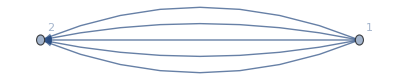

1+1/y^4+1/y^2+y^2+y^4

I_reg = 1+1/y^4+1/y^2+y^2+y^4

I_tot = 1+1/y^4+1/y^2+y^2+y^4

```mathematica
Nvec={1,1};
Mat={{0,5},{-5,0}};
m=Length[Mat];
QuiverPlot[Mat]
PMat=Mat;
Cvec={1,-1};
RMat={{0,0},{0,0}};
CoulombIndex[Mat,PMat,Cvec,y]//Simplify
Itot=ExtendedCoulombIndex[Mat,PMat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

# 3 centers 1 Loop

## An example obeying triangular inequalities

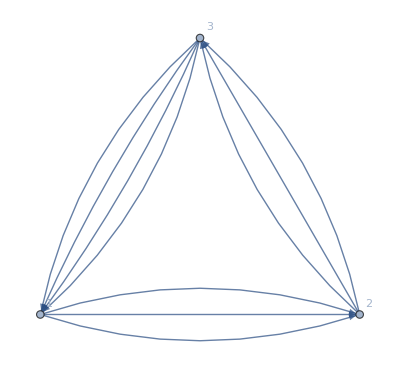

(1+y^4)/((-1+y^2)^2)

I_reg = (1+y^4)/((-1+y^2)^2)

I_{{1,2,3}} = (5-12 y^2+5 y^4)/((-1+y^2)^2)

I_tot = 6

```mathematica
Nvec={1,1,1};
Mat={{0,3,-4},{-3,0,3},{4,-3,0}};
QuiverPlot[Mat]
Cvec={1,1,-2};
m=Length[Cvec];
RMat={{0,2/3,-2/3},{-2/3,0,2/3},{2/3,-2/3,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

## An example violating triangular inequalities

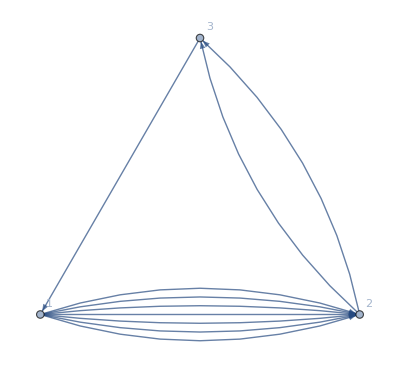

((1+y^2)^2 (1+y^4+y^8))/y^6

I_reg = ((1+y^2)^2 (1+y^4+y^8))/y^6

I_{{1,2,3}} = 0

I_tot = ((1+y^2)^2 (1+y^4+y^8))/y^6

```mathematica
Nvec={1,1,1};
Mat={{0,7,-1},{-7,0,2},{1,-2,0}};
QuiverPlot[Mat]
Cvec={1,1,-2};
RMat={{0,2/3,-2/3},{-2/3,0,2/3},{2/3,-2/3,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

# 4 centers

## example with no oriented cycles

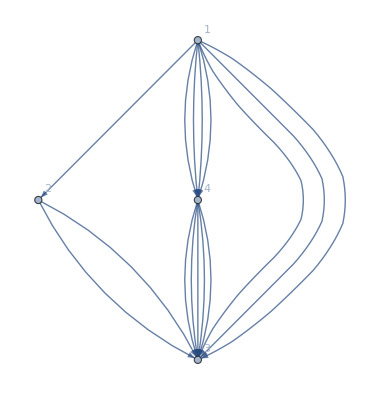

((1+y^2)^2 (1+y^4) (1-y+y^2-y^3+y^4) (1+y+y^2+y^3+y^4) (1+y^8))/y^12

I_reg = ((1+y^2)^2 (1+y^2+2 y^4+2 y^6+3 y^8+2 y^10+3 y^12+2 y^14+2 y^16+y^18+y^20))/y^12

I_tot = ((1+y^2)^2 (1+y^2+2 y^4+2 y^6+3 y^8+2 y^10+3 y^12+2 y^14+2 y^16+y^18+y^20))/y^12

```mathematica
Nvec={1,1,1,1};
Mat={{0,1,3,4},{-1,0,2,0},{-3,-2,0,-5},{-4,0,5,0}};
QuiverPlot[Mat]
Cvec={1,2,-6,3};
RMat={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
Simplify[CoulombBranchFormula[Mat,Cvec,Nvec]-Plus@@Itot]
```

0

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

## cyclic quiver obeying inequalities

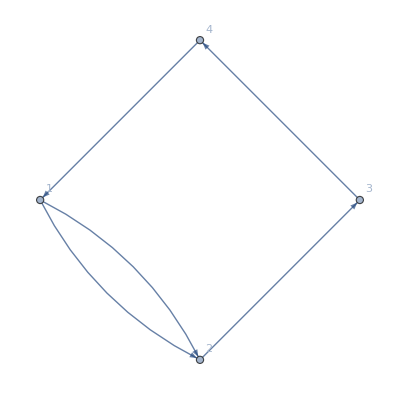

(1-y^2+y^4)/((-1+y^2)^2)

I_reg = (1-y^2+y^4)/((-1+y^2)^2)

I_{{1,2,3,4}} = -y^2/((-1+y^2)^2)

I_tot = 1

```mathematica
Nvec={1,1,1,1};
Mat=CyclicQuiverDSZ[{2,1,1,1}];
m=Length[Mat];
QuiverPlot[Mat]
Cvec={1,2,-6,3};
RMat={{0,2,0,0},{-2,0,0,0},{0,0,0,0},{0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

## 4 node quiver with 2 loops

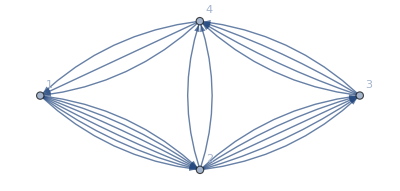

-(1+y^2+y^4+y^10+y^12+y^14)/(y^5 (-1+y^2)^2)

I_reg = -(1+y^2+y^4+y^10+y^12+y^14)/(y^5 (-1+y^2)^2)

I_{{1,2,3,4}} = (-230-2207 y^2+5101 y^4+y^6-5101 y^8+2207 y^10+230 y^12)/(y^3 (-1+y^2)^3)

I_{{1,2,4}} = -y^3/((-1+y^2)^3)

I_tot = -1/y^5+227/y^3+2891/y+2891 y+227 y^3-y^5

```mathematica
Nvec={1,1,1,1};
a={6,5,4,3,2};
Mat={{0,a[[1]],0,-a[[4]]},{-a[[1]],0,a[[2]],a[[5]]},{0,-a[[2]],0,a[[3]]},{a[[4]],-a[[5]],-a[[3]],0}};
QuiverPlot[Mat]
Cvec={1,2,-6,3};
RMat={{0,2,0,0},{-2,0,0,0},{0,0,0,0},{0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
ListLoopRCharges[Mat,RMat]
```

{{{1,2,4},2},{{1,2,3,4},2}}

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

# 5 Center

## 1 Loop

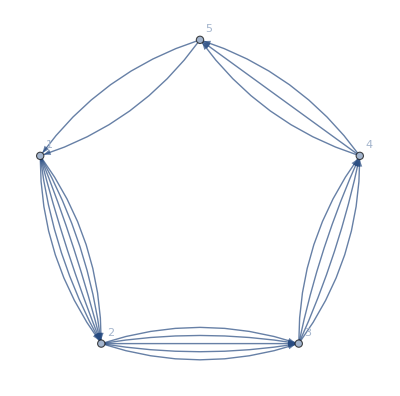

-(-1+y^4+y^6+y^18+y^20-y^24)/(y^8 (-1+y^2)^4)

I_reg = -(-1+y^4+y^6+y^10+y^14+y^18+y^20-y^24)/(y^8 (-1+y^2)^4)

I_{{2,4}} = (y^2+y^6)/((-1+y^2)^4)

I_{{1,2,3,4,5}} = (1924+29695 y^2-43809 y^4-122814 y^6+270010 y^8-122814 y^10-43809 y^12+29695 y^14+1924 y^16)/(y^4 (-1+y^2)^4)

I_tot = 94232+1/y^8+4/y^6+1933/y^4+37406/y^2+37406 y^2+1933 y^4+4 y^6+y^8

```mathematica
Nvec={1,1,1,1,1};
Mat=CyclicQuiverDSZ[{6,5,4,3,2}];
QuiverPlot[Mat]
Cvec={1,2,-10,3,4};
RMat={{0,2,0,0,0},{-2,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

In some special cases there exist “regular” solution where center collide. To get the right counting we perturb the matrix Mat but they still need to be close and can’t be distinguished from scaling solution which characteristic is to be of order r. Therefore the decomposition ("I")_("reg") , ("I")_("{{2,4}}),..., cannot be trusted anymore. Hence the difference with CoulombIndex.

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

## 5-node quiver with 2 loops

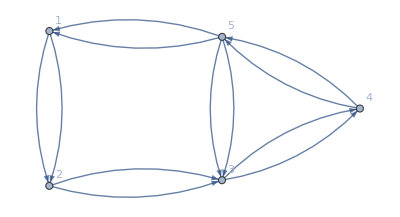

((1+y^2)^2)/((-1+y^2)^2)

```mathematica
Nvec={1,1,1,1,1};
a=2{1,1,1,1,1,1};
Mat={{0,a[[1]],0,0,-a[[5]]},{-a[[1]],0,a[[2]],0,0},{0,-a[[2]],0,a[[3]],-a[[6]]},{0,0,-a[[3]],0,a[[4]]},{a[[5]],0,a[[6]],-a[[4]],0}};
QuiverPlot[Mat]
Cvec={3,2,3,4,-12};
RMat={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,2,0},{0,0,-2,0,0},{0,0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
```

```mathematica
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

I_reg = (1+y^8)/((-1+y^2)^4)

I_{{2,3,4,5}} = y^4/((-1+y^2)^4)

I_{{3,4,5}} = (1-4 y^2+2 y^4-4 y^6+y^8)/((-1+y^2)^4)

I_{{1,2,3,4,5}} = (2-12 y^2+21 y^4-12 y^6+2 y^8)/((-1+y^2)^4)

I_tot = 4

In some special cases there exist “regular” solution where center collide. To get the right counting we perturb the matrix Mat but they still need to be close and can’t be distinguished from scaling solution which characteristic is to be of order r. Therefore the decomposition ("I")_("reg") , ("I")_("{{2,3,4,5}}),..., cannot be trusted anymore. Hence the difference with CoulombIndex.

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

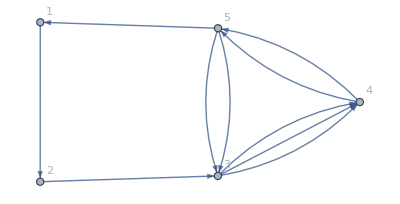

(1-2 y^2-2 y^6+y^8)/((-1+y^2)^4)

```mathematica
Nvec={1,1,1,1,1};
a={1,1,3,2,1,2};
Mat={{0,a[[1]],0,0,-a[[5]]},{-a[[1]],0,a[[2]],0,0},{0,-a[[2]],0,a[[3]],-a[[6]]},{0,0,-a[[3]],0,a[[4]]},{a[[5]],0,a[[6]],-a[[4]],0}};
QuiverPlot[Mat]
Cvec={1,1,1,1,-4};
RMat={{0,0,0,0,0},{0,0,0,0,0},{0,0,0,2,0},{0,0,-2,0,0},{0,0,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
```

```mathematica
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r/2,y];
```

I_reg = (1-2 y^2-2 y^6+y^8)/((-1+y^2)^4)

I_{{3,4,5}} = -((y+y^3)^2)/((-1+y^2)^4)

I_{{1,2,3,4,5}} = (2-9 y^2+20 y^4-9 y^6+2 y^8)/((-1+y^2)^4)

I_tot = 3

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

# 4 center 3 loops From BH and Quiver (arxiv : 1207.2230)

## 5.1.1 Example with only 3-center scaling solutions

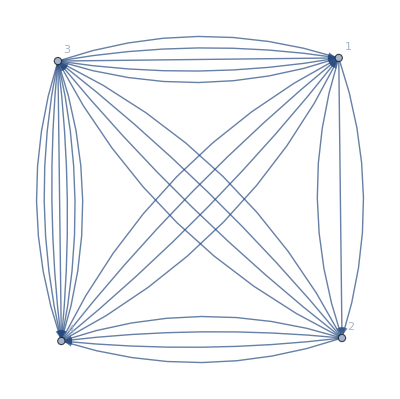

(1+y^2+2 y^4+2 y^6+2 y^8+2 y^10+2 y^12+y^14+y^16)/(y^6 (-1+y^2)^2)

I_reg = (1+y^2+2 y^4+2 y^6+2 y^8+2 y^10+2 y^12+y^14+y^16)/(y^6 (-1+y^2)^2)

I_{{1,2,3}} = -(-9+11 y^2+2 y^4+2 y^6+2 y^8+2 y^10+2 y^12+11 y^14-9 y^16)/(y^6 (-1+y^2)^2)

I_{{1,2,3,4}} = 0

I_tot = (10 (1+y^2+y^4+y^6+y^8+y^10+y^12))/y^6

```mathematica
Nvec={1,1,1,1};
a={3,4,7,4,5,4};
Mat={{0,a[[1]],-a[[5]],-a[[4]]},{-a[[1]],0,a[[2]],a[[6]]},{a[[5]],-a[[2]],0,a[[3]]},{a[[4]],-a[[6]],-a[[3]],0}};
QuiverPlot[Mat]
Cvec={21/10,3,-11/10,-4};
RMat={{0,0,-2,-2},{0,0,0,0},{2,0,0,0},{2,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0

#### eq 3.35

```mathematica
oms=CyclicQuiverOmS[{a[[1]],a[[2]],a[[5]]},y]
```

9

#### eq 5.12

```mathematica
(y^(-6)+y^(-4)+y^(-2)+1+y^2+y^4 +y^6)(oms+1^2)
```

10 (1+1/y^6+1/y^4+1/y^2+y^2+y^4+y^6)

## generic 4-center with scaling solutions

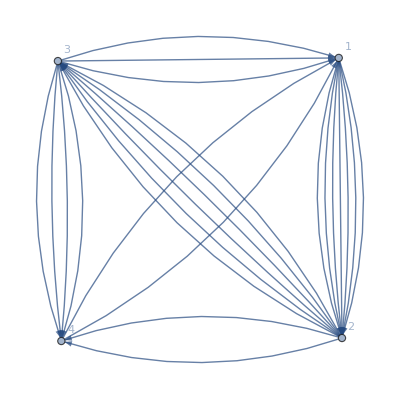

-((1+y^2) (1+y^8))/(y^3 (-1+y^2)^2)

I_reg = -(1+y^2+y^8+y^10)/(y^3 (-1+y^2)^2)

I_{{1,2,3,4}} = (353+3428 y^2-3779 y^4-3779 y^6+3428 y^8+353 y^10)/(y^3 (-1+y^2)^2)

I_tot = 352/y^3+4131/y+4131 y+352 y^3

```mathematica
Nvec={1,1,1,1};
a={7,6,4,2,3,2};
Mat={{0,a[[1]],-a[[5]],-a[[4]]},{-a[[1]],0,a[[2]],a[[6]]},{a[[5]],-a[[2]],0,a[[3]]},{a[[4]],-a[[6]],-a[[3]],0}};
QuiverPlot[Mat]
Cvec={2,3,-6,1};
RMat={{0,0,-2,-2},{0,0,0,0},{2,0,0,0},{2,0,0,0}};
CoulombIndex[Mat,Mat,Cvec,y]//Factor//Simplify
Itot=ExtendedCoulombIndex[Mat,Mat,RMat,Cvec,-r,y];
```

```mathematica
JKInitialize[Mat,RMat,Cvec,Nvec]
Simplify[Plus@@JKIndex[JKChargeMatrix,Nvec,JKEta]-Plus@@Itot]
```

1 stable flags in total

From computing the Euler number, 1 stable flags appear to contribute

0